## Conic Sections

```mathematica
(* declaring variables  *)
h=1;
μ=1;
a=h^2/μ;
shape[e_]:=PolarPlot[a/(1+e*Cos[θ]),{θ,0,2π},PlotStyle->{Red,Thin}];
point:=Graphics[{{Red,PointSize[.01],Point[{0,0}]},{FontSize->10,Green,Text["Focal Point",{0,a/10}]}}];
point2[e_]:=Graphics[{{Red,PointSize[.01],Point[{(-2a e)/(1-e^2),0}]},{FontSize->10,Green,Text["Focal Point",{(-2a e)/(1-e^2),a/10}]}}];
apse[e_]:=Graphics[Line[{{a/(1+e),0},{-a/(1-e),0}}]];
Manipulate[
Show[{point,point2[e],shape[e],apse[e]},
{PlotRange->3a*{{-1,1},{-1,1}},ImageSize->Large,PlotLabel->" Conic Sections",
BaseStyle->{FontWeight->"Bold",FontSize->12}}]
,{e,0,2}]
```

## Book Example

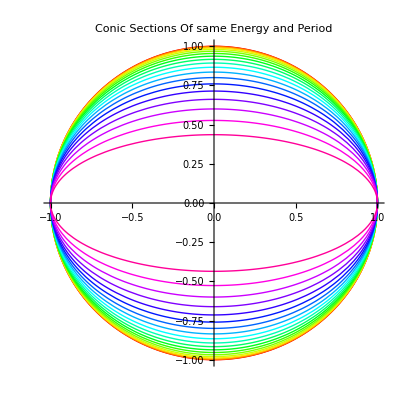

```mathematica
(* declaring variables  *)
h=1;
μ=1;
a=h^2/μ;
shape1[e_,color_]:=ParametricPlot[(1-e^2)*{(a*Cos[θ])/(1+e*Cos[θ])+(a e)/(1-e^2),(a*Sin[θ])/(1+e*Cos[θ])},{θ,0,2π},PlotStyle->{color,Thin}];
Show[Table[shape1[e,Hue[e]],{e,0,0.9,0.05}],{PlotRange->a*{{-1,1},{-1,1}},PlotLabel->"Conic Sections Of same Energy and Period",BaseStyle->{FontSize->14}}]
```